```mathematica
BooleanTable[{p,q,p||q},{p,q}]//Boole//TableForm
```

1 | 1 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

```mathematica
BooleanTable[{p,q,Xor[p,q]},{p,q}]//Boole//TableForm
```

1 | 1 | 0
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

```mathematica
myFunc[x_]:= BooleanTable[{p,q,x[p,q]},{p,q}]//Boole//TableForm
```

```mathematica
f=Or
```

Or

```mathematica
myFunc[And]
```

1 | 1 | 1
1 | 0 | 0
0 | 1 | 0
0 | 0 | 0

```mathematica
Manipulate[myFunc[f],{f, {And, Or, Xor, Nand}}]
```

```mathematica
BooleanMinimize[And[Or[p,q], Xor[q,p]]]//FullSimplify//FullForm
```

Xor[p,q]

```mathematica
BooleanTable[{p,q,And[Or[p,q], Xor[q,p]]},{p,q}]//Boole//TableForm
```

1 | 1 | 0
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

```mathematica
BooleanMinimize[And[Or[p,q], Xor[q,p]]]//FullForm
```

Or[And[p,Not[q]],And[Not[p],q]]

BooleanTable[{p, q, p || q}, {p, q}] // Boole

```mathematica
BooleanTable[{p,q,p||q},{p,q}]//Boole//Grid
```

1 | 1 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

```mathematica
Grid[BooleanTable[{p,q,p||q},{p,q}]//Boole, Frame -> All,Background->{{None, None, Gray},{LightGray, None}}]
```

1 | 1 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

```mathematica
Insert[BooleanTable[{p,q,p||q},{p,q}]//Boole,{a,b,out}, 1]//TableForm
```

a | b | out
1 | 1 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

Grid[BooleanTable[{p, q, p || q}, {p, q}] // Boole, Frame -> All, Background -> {{None, None, Gray}, {LightGray, None}}]

```mathematica
Grid[Insert[BooleanTable[{p,q,p||q},{p,q}]//Boole,{a,b,out}, 1],Spacings -> {2, 1}, Frame -> All,Background->{{None, None, Gray},{LightGray, None}}]
```

a | b | out
1 | 1 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

```mathematica
First[Grid[{{a,b,out},{1,1,1},{1,0,1},{0,1,1},{0,0,0}},Spacings->{2,1},Frame->All,Background->{{None,None,GrayLevel[0.5]},{GrayLevel[0.85],None}}]]
```

{{a,b,out},{1,1,1},{1,0,1},{0,1,1},{0,0,0}}

```mathematica
Grid[Insert[BooleanTable[{p,Not[p]},{p}]//Boole,{in,out}, 1],Spacings -> {2, 1}, Frame -> All,Background->{{None, None, Gray},{LightGray, None}}]
```

in | out
1 | 0
0 | 1

```mathematica
Or[And[A, Not[B],C] , And[A, B,C], And[A,C], And[A,B,Not[C]]] //FullSimplify
```

A&&(B||C)

Grid[Insert[BooleanTable[{p, q, p || q}, {p, q}] // Boole, {a, b, out}, 1], Spacings -> {2, 1}, Frame -> All, Background -> {{None, None, Gray}, {LightGray, None}}]

```mathematica
Grid[{{a,b,c,out},{1,1,1},{1,0,1},{0,1,1},{0,0,0}},Spacings->{2,1},Frame->All,Background->{{None,None,GrayLevel[0.5]},{GrayLevel[0.85],None}}]
```

a | b | out
1 | 1 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

```mathematica
BooleanTable[{A, B,C, A&&(B||C))||(B&&C))}, {A,B,C}]//Boole//MatrixForm
```

```mathematica
Clear[c]
```

```mathematica
Or[And[A, C], And[B, C], And[A, B]]//FullSimplify
```

(A&&(B||C))||(B&&C)

```mathematica
Grid[Insert[BooleanTable[{A,B,C,(A&&(B||C))||(B&&C) }, {A,B,C}] // Boole, {a, b,c, out}, 1], Spacings -> {2, 1}, Frame -> All, Background -> {{None, None, Gray}, {LightGray, None}}]
```

a | b | c | out
1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

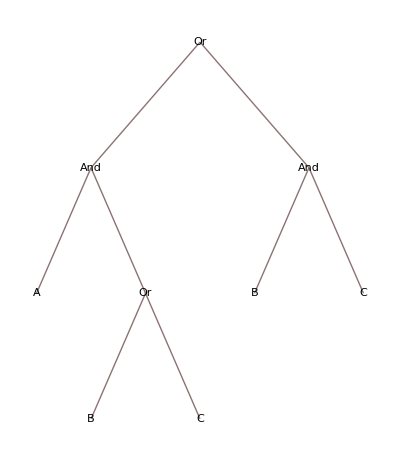

```mathematica
(A && (B || C)) || (B && C) //TreeForm
```

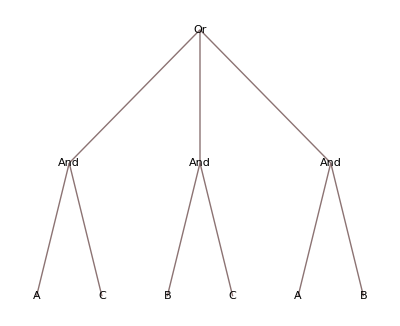

```mathematica
Or[And[A, C], And[B, C], And[A, B]]//TreeForm
```